```mathematica
ClearAll["Global`*"]
```

```mathematica
(*The equations that I want to solve are
B-A=\tilde{a}(x)n,   λ*B+(1-λ)*A=I+b(x)m
We set A=Subscript[Q, 1] Subscript[U, 1] and B=Subscript[Q, 2] Subscript[U, 2], we get
Subscript[Q, 2] Subscript[U, 2]-Subscript[Q, 1] Subscript[U, 1]=\tilde{a}(x)n,    λ*Subscript[Q, 2] Subscript[U, 2]+(1-λ)*Subscript[Q, 1] Subscript[U, 1]=I+b(x)m=Subscript[Q, 1] Subscript[U, 1]+λ*\tilde{a}(x)n,
where we have used the first equation to simplify the second equation.
We let Subscript[Q, 2]=Subscript[Q, 1]*Q and Subscript[Q, 1] a=\tilde{a}, then we get
Subscript[QU, 2]-Subscript[U, 1]=a(x)n,    Subscript[U, 1]+λ*a(x)n=Subscript[Q, 1]^T(I+b(x)m)
We must note that since the two variants are symmetry related, we have the relation Subscript[U, 2]=Subscript[R, 2]^T Subscript[U, 1] Subscript[R, 2].
Q Subscript[R, 2]^T Subscript[U, 1] Subscript[R, 2]-Subscript[U, 1]=a(x)n,      Subscript[U, 1]+λ*a(x)n=Subscript[Q, 1]^T(I+b(x)m)
We will further use the fact that 
Subscript[U, 1]=diag(Subscript[η, 2],Subscript[η, 1],Subscript[η, 1]),   Subscript[U, 2]=diag(Subscript[η, 1],Subscript[η, 2],Subscript[η, 1])
*)
```

```mathematica
(*We will First check the Twining condition of the two MArtensite Variants.
We have an equation of the Form 
QF-G=a(x)n 
with F\mapsto Subscript[U, 2], G\mapsto Subscript[U, 1]. According to Bhattacharya, the Solution to the above corresponds to having middle eigen value 1 for 
C=G^-T F^T FG^-1.
The vectors a and n are determined the eigen values and eigen vectors of C.*)
```

```mathematica
Q:={{Q11,Q12,Q13},{Q21,Q22,Q23},{Q31,Q32,Q33}}
```

```mathematica
Subscript[UU, 2][Subscript[η, 1]_,Subscript[η, 2]_]:={{Subscript[η, 1],0,0},{0,Subscript[η, 2],0},{0,0,Subscript[η, 1]}}
```

```mathematica
Subscript[UU, 1][Subscript[η, 1]_,Subscript[η, 2]_]:={{Subscript[η, 2],0,0},{0,Subscript[η, 1],0},{0,0,Subscript[η, 1]}}
```

```mathematica
MatrixForm[Subscript[UU, 1][Subscript[η, 1],Subscript[η, 2]]]
```

(η_2 | 0 | 0
0 | η_1 | 0
0 | 0 | η_1)

```mathematica
Q.Q//MatrixForm(*Testing MAtrix Multipication*)
```

(Q11^2+Q12 Q21+Q13 Q31 | Q11 Q12+Q12 Q22+Q13 Q32 | Q11 Q13+Q12 Q23+Q13 Q33
Q11 Q21+Q21 Q22+Q23 Q31 | Q12 Q21+Q22^2+Q23 Q32 | Q13 Q21+Q22 Q23+Q23 Q33
Q11 Q31+Q21 Q32+Q31 Q33 | Q12 Q31+Q22 Q32+Q32 Q33 | Q13 Q31+Q23 Q32+Q33^2)

```mathematica
Q.{{1},{2},{3}}//MatrixForm
```

(Q11+2 Q12+3 Q13
Q21+2 Q22+3 Q23
Q31+2 Q32+3 Q33)

```mathematica
CCe[Subscript[η, 1]_,Subscript[η, 2]_]:=Inverse[Transpose[Subscript[UU, 1][Subscript[η, 1],Subscript[η, 2]]]]*Transpose[Subscript[UU, 2][Subscript[η, 1],Subscript[η, 2]]]*Subscript[UU, 2][Subscript[η, 1],Subscript[η, 2]]*Inverse[Subscript[UU, 1][Subscript[η, 1],Subscript[η, 2]]]
```

```mathematica
Inverse[Transpose[Subscript[UU, 1][Subscript[η, 1],Subscript[η, 2]]]]*Transpose[Subscript[UU, 2][Subscript[η, 1],Subscript[η, 2]]]*Subscript[UU, 2][Subscript[η, 1],Subscript[η, 2]]*Inverse[Subscript[UU, 1][Subscript[η, 1],Subscript[η, 2]]]//MatrixForm
```

(η_1^2/η_2^2 | 0 | 0
0 | η_2^2/η_1^2 | 0
0 | 0 | 1)

```mathematica
(*Assuming Subscript[η, 1]<Subscript[η, 2], we get *)
```

```mathematica
Subscript[aa, plus][Subscript[η, 1]_,Subscript[η, 2]_]:=Sqrt[2]*(Subscript[η, 2]^2-Subscript[η, 1]^2)/(Subscript[η, 2]^2+Subscript[η, 1]^2)*{{Subscript[η, 2]},{Subscript[η, 1]},{0}}
```

```mathematica
Subscript[nn, plus][Subscript[η, 1]_,Subscript[η, 2]_]:=1/Sqrt[2]*{{-1},{1},{0}}
```

```mathematica
Subscript[aa, minus][Subscript[η, 1]_,Subscript[η, 2]_]:=Sqrt[2]*(Subscript[η, 2]^2-Subscript[η, 1]^2)/(Subscript[η, 2]^2+Subscript[η, 1]^2)*{{Subscript[η, 2]},{-Subscript[η, 1]},{0}}
```

```mathematica
Subscript[nn, minus][Subscript[η, 1]_,Subscript[η, 2]_]:=1/Sqrt[2]*{{-1},{-1},{0}}
```

```mathematica
Subscript[aa, plus][Subscript[η, 1],Subscript[η, 2]]
```

aa_plus[η_1,η_2]

```mathematica
(*We now Focus on the second Equation. The conditions for the twinned interface is
δ<=-2,      Subscript[trU, 0]^2-Subscript[detU, 0]^2-2+1/(2*δ)*|a|^2>=0
where δ=a.Subscript[U, 0](Subscript[U, 0]^2-I)^-1 n
*)
```

```mathematica
(Subscript[UU, 1][Subscript[η, 1],Subscript[η, 2]])^2-IdentityMatrix[3]//MatrixForm
```

(-1+η_2^2 | 0 | 0
0 | -1+η_1^2 | 0
0 | 0 | -1+η_1^2)

```mathematica
Simplify[Inverse[(Subscript[UU, 1][Subscript[η, 1],Subscript[η, 2]])^2-IdentityMatrix[3]]]//MatrixForm
```

(1/(-1+η_2^2) | 0 | 0
0 | 1/(-1+η_1^2) | 0
0 | 0 | 1/(-1+η_1^2))

```mathematica
Simplify[Subscript[UU, 1][Subscript[η, 1],Subscript[η, 2]].Inverse[(Subscript[UU, 1][Subscript[η, 1],Subscript[η, 2]])^2-IdentityMatrix[3]]]//MatrixForm
```

(η_2/(-1+η_2^2) | 0 | 0
0 | η_1/(-1+η_1^2) | 0
0 | 0 | η_1/(-1+η_1^2))

```mathematica
Simplify[Subscript[UU, 1][Subscript[η, 1],Subscript[η, 2]].Inverse[(Subscript[UU, 1][Subscript[η, 1],Subscript[η, 2]])^2-IdentityMatrix[3]].{{-1/Sqrt[2]},{1/Sqrt[2]},{0}}]//MatrixForm
```

(η_2/(√2 (1-η_2^2))
η_1/(√2 (-1+η_1^2))
0)

```mathematica
Transpose[{{-1/Sqrt[2]},{1/Sqrt[2]},{0}}].{{-1/Sqrt[2]},{1/Sqrt[2]},{0}}(*Testing Dot product in MAtehmatica*)
```

{{1}}

```mathematica
Simplify[Transpose[Sqrt[2]*(Subscript[η, 2]^2-Subscript[η, 1]^2)/(Subscript[η, 2]^2+Subscript[η, 1]^2)*{{Subscript[η, 2]},{Subscript[η, 1]},{0}}].Subscript[U, 1].Inverse[Subscript[U, 1]^2-IdentityMatrix[3]].{{-1/Sqrt[2]},{1/Sqrt[2]},{0}}]
```

{{((η_1^2-η_2^2)^2)/((-1+η_1^2) (-1+η_2^2) (η_1^2+η_2^2))}}

```mathematica
Simplify[Transpose[Sqrt[2]*(Subscript[η, 2]^2-Subscript[η, 1]^2)/(Subscript[η, 2]^2+Subscript[η, 1]^2)*{{Subscript[η, 2]},{-Subscript[η, 1]},{0}}].Subscript[U, 1].Inverse[Subscript[U, 1]^2-IdentityMatrix[3]].{{-1/Sqrt[2]},{-1/Sqrt[2]},{0}}]
```

{{((η_1^2-η_2^2)^2)/((-1+η_1^2) (-1+η_2^2) (η_1^2+η_2^2))}}

```mathematica
δi[Subscript[η, 1]_,Subscript[η, 2]_]:=Transpose[Sqrt[2]*(Subscript[η, 2]^2-Subscript[η, 1]^2)/(Subscript[η, 2]^2+Subscript[η, 1]^2)*{{Subscript[η, 2]},{Subscript[η, 1]},{0}}].Subscript[U, 1].Inverse[Subscript[U, 1]^2-IdentityMatrix[3]].{{-1/Sqrt[2]},{1/Sqrt[2]},{0}}
```

```mathematica
Simplify[δi[Subscript[η, 1],Subscript[η, 2]]]
```

δi[η_1,η_2]

```mathematica
(*We now check the other inequality, we have
Subscript[trU, 0]^2-Subscript[detU, 0]^2-2+1/(2*δ)*|a|^2*)
```

```mathematica
Tr[(Subscript[UU, 1][Subscript[η, 1],Subscript[η, 2]])^2](*Testing out the Trace of a Matrix in MAtehmatica*)
```

2 η_1^2+η_2^2

```mathematica
Det[(Subscript[UU, 1][Subscript[η, 1],Subscript[η, 2]])^2](*Testing out The Determinant in MAthematica*)
```

η_1^4 η_2^2

```mathematica
Simplify[Transpose[{{Sqrt[2]*(Subscript[η, 2]^2-Subscript[η, 1]^2)/(Subscript[η, 2]^2+Subscript[η, 1]^2)*Subscript[η, 2]},{-Sqrt[2]*(Subscript[η, 2]^2-Subscript[η, 1]^2)/(Subscript[η, 2]^2+Subscript[η, 1]^2)*Subscript[η, 1]},{0}}].{{Sqrt[2]*(Subscript[η, 2]^2-Subscript[η, 1]^2)/(Subscript[η, 2]^2+Subscript[η, 1]^2)*Subscript[η, 2]},{-Sqrt[2]*(Subscript[η, 2]^2-Subscript[η, 1]^2)/(Subscript[η, 2]^2+Subscript[η, 1]^2)*Subscript[η, 1]},{0}}]
```

{{(2 (η_1^2-η_2^2)^2)/(η_1^2+η_2^2)}}

```mathematica
Simplify[Tr[(Subscript[UU, 1][Subscript[η, 1],Subscript[η, 2]])^2]-Det[(Subscript[UU, 1][Subscript[η, 1],Subscript[η, 2]])^2]-2+((2 (Subscript[η, 1]^2-Subscript[η, 2]^2)^2)/(Subscript[η, 1]^2+Subscript[η, 2]^2))/(2*((Subscript[η, 1]^2-Subscript[η, 2]^2)^2)/((-1+Subscript[η, 1]^2) (-1+Subscript[η, 2]^2) (Subscript[η, 1]^2+Subscript[η, 2]^2)))]
```

-((-1+η_1^2) (-1+η_1^2 η_2^2))

```mathematica
(*We will plot all the different inequalities*)
```

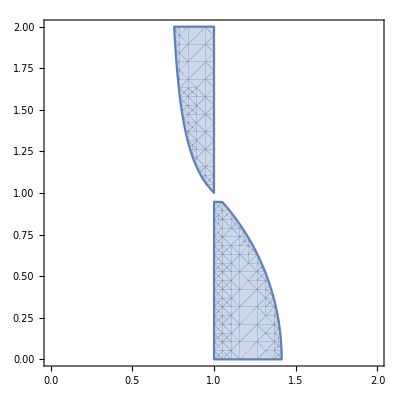

```mathematica
RegionPlot[{(1-Subscript[η, 1]^2) (-1+Subscript[η, 1]^2 Subscript[η, 2]^2)>0&&((Subscript[η, 1]^2-Subscript[η, 2]^2)^2)/((-1+Subscript[η, 1]^2) (-1+Subscript[η, 2]^2) (Subscript[η, 1]^2+Subscript[η, 2]^2))<=-2},{Subscript[η, 1],0,2},{Subscript[η, 2],0,2},PlotLegends->"Expressions"]
```

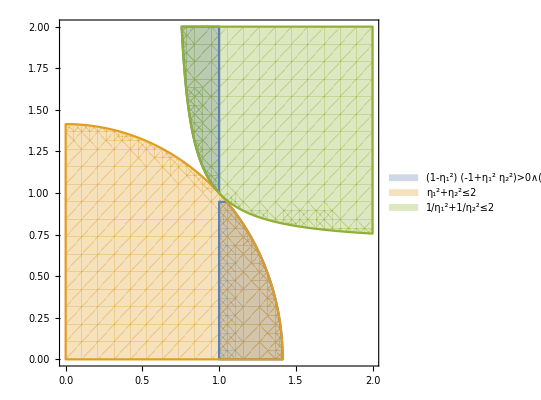

```mathematica
RegionPlot[{(1-Subscript[η, 1]^2) (-1+Subscript[η, 1]^2 Subscript[η, 2]^2)>0&&((Subscript[η, 1]^2-Subscript[η, 2]^2)^2)/((-1+Subscript[η, 1]^2) (-1+Subscript[η, 2]^2) (Subscript[η, 1]^2+Subscript[η, 2]^2))<=-2,Subscript[η, 1]^2+Subscript[η, 2]^2<=2,Subscript[η, 1]^-2+Subscript[η, 2]^-2<=2},{Subscript[η, 1],0,2},{Subscript[η, 2],0,2},PlotLegends->"Expressions"]
```

```mathematica
(*We can solve the two inequalitites separately, We focus on the first inequality can be solved for the following two conditions
Subscript[η, 1]<1<1/Subscript[η, 1]<Subscript[η, 2] or Subscript[η, 1]>1>1/Subscript[η, 1]>Subscript[η, 2].
These will be termed Case 1 and Case 2 respectively.
*)
```

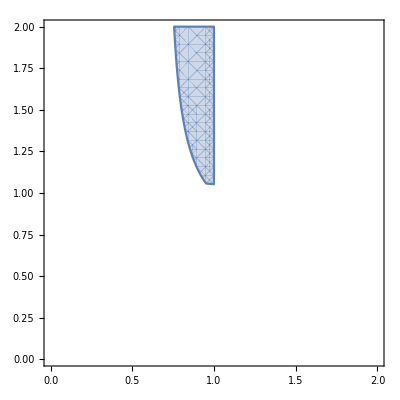

```mathematica
RegionPlot[{Subscript[η, 1]<1&&Subscript[η, 2]*Subscript[η, 1]>1&&((Subscript[η, 1]^2-Subscript[η, 2]^2)^2)/((1-Subscript[η, 1]^2) (-1+Subscript[η, 2]^2) (Subscript[η, 1]^2+Subscript[η, 2]^2))>=2},{Subscript[η, 1],0,2},{Subscript[η, 2],0,2},PlotLegends->"Expressions"](*Case 1 *)
```

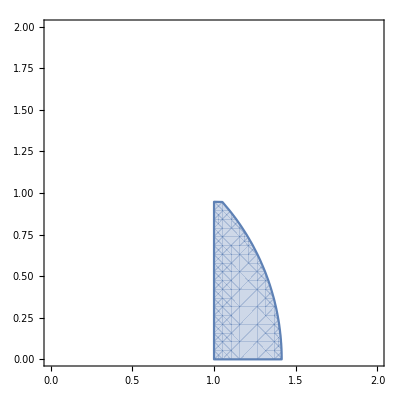

```mathematica
RegionPlot[{Subscript[η, 1]>1&&Subscript[η, 2]*Subscript[η, 1]<1&&((Subscript[η, 1]^2-Subscript[η, 2]^2)^2)/((-1+Subscript[η, 1]^2) (-1+Subscript[η, 2]^2) (Subscript[η, 1]^2+Subscript[η, 2]^2))<=-2},{Subscript[η, 1],0,2},{Subscript[η, 2],0,2},PlotLegends->"Expressions"](*Case 2*)
```

```mathematica
Expand[(Subscript[η, 1]^2-Subscript[η, 2]^2)^2-2*(1-Subscript[η, 1]^2) (-1+Subscript[η, 2]^2) (Subscript[η, 1]^2+Subscript[η, 2]^2)]
```

2 η_1^2-η_1^4+2 η_2^2-6 η_1^2 η_2^2+2 η_1^4 η_2^2-η_2^4+2 η_1^2 η_2^4